# AntonAntonov/OutlierIdentifiers

Outlier identifier functions

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"BottomOutliers.nb"DocumentationEnglishReferencePagesSymbolsBottomOutliers.nb

"ColorPlotOutliers.nb"DocumentationEnglishReferencePagesSymbolsColorPlotOutliers.nb

"HampelIdentifier.nb"DocumentationEnglishReferencePagesSymbolsHampelIdentifier.nb

"HampelIdentifierParameters.nb"DocumentationEnglishReferencePagesSymbolsHampelIdentifierParameters.nb

"ListPlotOutliers.nb"DocumentationEnglishReferencePagesSymbolsListPlotOutliers.nb

"OutlierIdentifier.nb"DocumentationEnglishReferencePagesSymbolsOutlierIdentifier.nb

"OutlierIdentifyLess.nb"DocumentationEnglishReferencePagesSymbolsOutlierIdentifyLess.nb

"OutlierIdentify.nb"DocumentationEnglishReferencePagesSymbolsOutlierIdentify.nb

"OutlierPosition.nb"DocumentationEnglishReferencePagesSymbolsOutlierPosition.nb

"QuartileIdentifier.nb"DocumentationEnglishReferencePagesSymbolsQuartileIdentifier.nb

"QuartileIdentifierParameters.nb"DocumentationEnglishReferencePagesSymbolsQuartileIdentifierParameters.nb

"SPLUSQuartileIdentifier.nb"DocumentationEnglishReferencePagesSymbolsSPLUSQuartileIdentifier.nb

"SPLUSQuartileIdentifierParameters.nb"DocumentationEnglishReferencePagesSymbolsSPLUSQuartileIdentifierParameters.nb

"TopOutliers.nb"DocumentationEnglishReferencePagesSymbolsTopOutliers.nb

"Tutorials"

"Kernel"

"OutlierIdentifiers.wl"KernelOutlierIdentifiers.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This paclet provides functions for detection and visualization of outliers in lists of numbers.

### Details

The purpose of the outlier detection algorithms is to find those elements in a list of numbers that have values significantly higher or lower than the rest of the values.

Taking a certain number of elements with the highest values is not the same as an outlier detection, but it can be used as a replacement.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`OutlierIdentifiers`"];
```

### Basic Examples

Let us consider the following set of 50 numbers:

```mathematica
SeedRandom[1232];
pnts=RandomVariate[GammaDistribution[5,1],50];
ResourceFunction["RecordsSummary"][pnts]
```

{1 column 1
Min | 0.43838
1st Qu | 3.36964
Median | 4.34468
Mean | 4.7455
3rd Qu | 6.42955
Max | 9.53163}

Here we find the outliers using the HampelIdentifierParameters function:

```mathematica
OutlierIdentify[pnts,HampelIdentifierParameters]
```

{6.6662,7.91273,8.47235,6.81757,1.75639,7.45096,8.24049,8.43018,0.43838,7.04841,8.20847,0.51827,9.53163}

Here we find the top outliers only:

```mathematica
OutlierIdentify[pnts,TopOutliers@*HampelIdentifierParameters]
```

{7.68192,8.47235,7.30092,6.97322,6.8833,7.1767,6.6981,7.20087,7.23864,6.75464,7.67918,6.57855,6.96975}

Here we find the top outliers positions:

```mathematica
OutlierPosition[pnts,TopOutliers@*HampelIdentifierParameters]
```

{3,4,6,8,13,26,34,37,38,41,42,47,48}

Here we plot the top outliers:

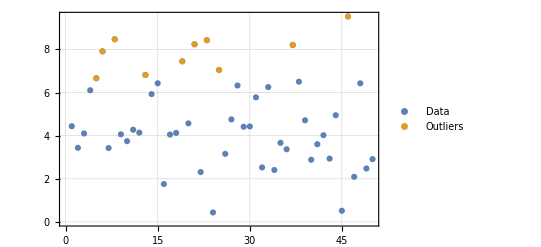

```mathematica
ListPlotOutliers[pnts,TopOutliers@*HampelIdentifierParameters,PlotTheme->"Detailed",PlotLegends->{"Data","Outliers"}]
```

### Scope

Here is the application of all outlier parameter finding functions in this paclet:

```mathematica
Association@Map[#->#[pnts]&,{HampelIdentifierParameters,SPLUSQuartileIdentifierParameters,QuartileIdentifierParameters}]
```

<|HampelIdentifierParameters→{2.08602,6.60334},SPLUSQuartileIdentifierParameters→{-1.22022,11.0194},QuartileIdentifierParameters→{1.21601,7.33582}|>

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-OutlierIdentifiers-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Identifier

Detection

Outlier

Hampel

SPLUS

Quartile

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

QuantileRegression

RecordsSummary

### Original Source References and Attributions

Ronald K. Pearson, "Mining Imperfect Data: Dealing with Contamination and Incomplete Records", 2005, SIAM.

Outlier detection in a list of numbers | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/OutlierIdentifiers.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

11.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.